```mathematica
(*X=10 Y=0.5 Yielding Physical states (and subsequently 3-entangled states) for t between 0 and 2pi*)
```

```mathematica
Table[Eigs[[1]],{t,0,2π,π/100}];
```

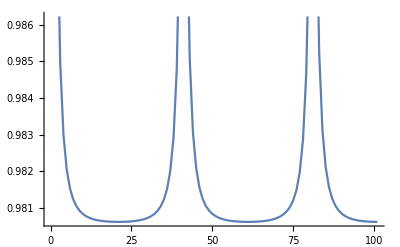

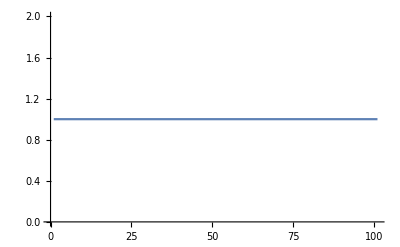

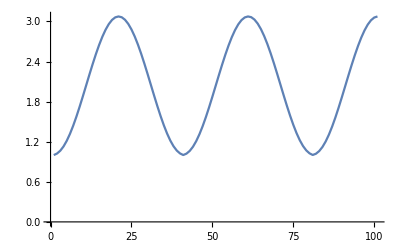

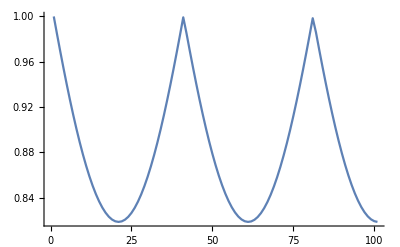

-Graphics-

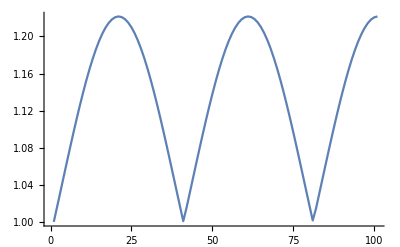

```mathematica
ListPlot[Table[Eigs[[1]],{t,0,π/2,π/200}],Joined->True]
ListPlot[Table[Eigs[[2]],{t,0,π/2,π/200}],Joined->True]
ListPlot[Table[Eigs[[3]],{t,0,π/2,π/200}],Joined->True]
ListPlot[Table[Eigs[[4]],{t,0,π/2,π/200}],Joined->True]
ListPlot[Table[Eigs[[5]],{t,0,π/2,π/200}],Joined->True]
ListPlot[Table[Eigs[[6]],{t,0,π/2,π/200}],Joined->True]
(*Checking first condition for Bona Fide C.M.; These eigenfunctions should be greater than 0 to be physical*)
```

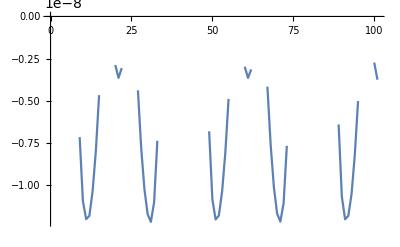

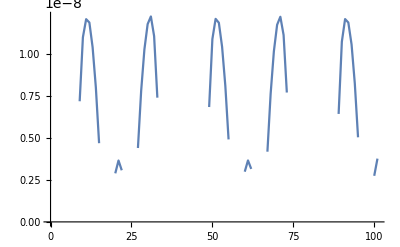

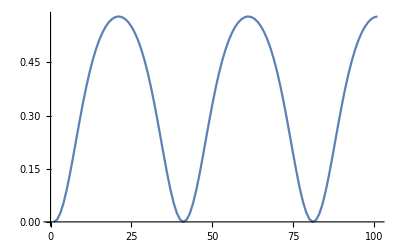

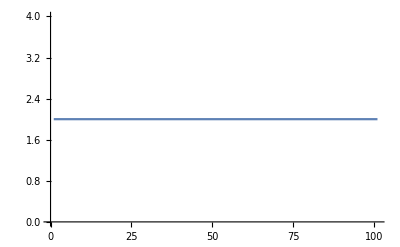

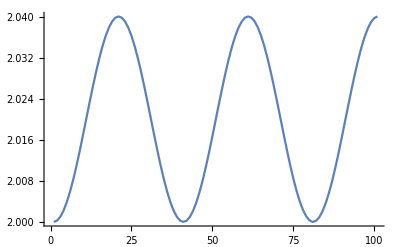

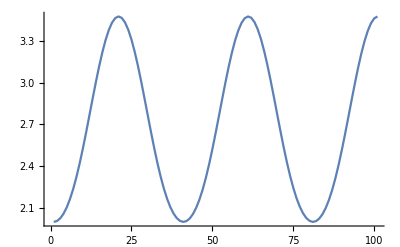

```mathematica
EigSymp=Eigenvalues[σ+ⅈ Σ];
ListPlot[Table[EigSymp[[1]],{t,0,π/2,π/200}],Joined->True]
ListPlot[Table[EigSymp[[2]],{t,0,π/2,π/200}],Joined->True]
ListPlot[Table[EigSymp[[3]],{t,0,π/2,π/200}],Joined->True]
ListPlot[Table[EigSymp[[4]],{t,0,π/2,π/200}],Joined->True]
ListPlot[Table[EigSymp[[5]],{t,0,π/2,π/200}],Joined->True]
ListPlot[Table[EigSymp[[6]],{t,0,π/2,π/200}],Joined->True]
(*Checking second condition for Bona Fide C.M.; These eigenfunctions should be also greater than 0 to be physical*)
```

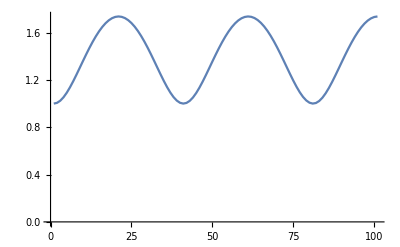

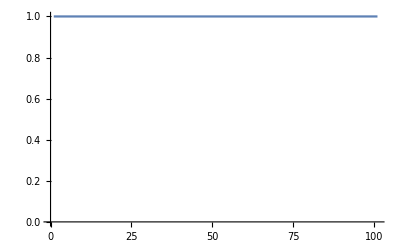

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
SympEig=Eigenvalues[ⅈ Σ . σ];
ListPlot[Table[Abs[SympEig[[1]]],{t,0,π/2,π/200}],Joined->True,PlotRange->{0,Automatic}]
ListPlot[Table[Abs[SympEig[[2]]],{t,0,π/2,π/200}],Joined->True,PlotRange->{0,Automatic}]
ListPlot[Table[Abs[SympEig[[3]]],{t,0,π/2,π/200}],Joined->True,PlotRange->{0,Automatic}]
ListPlot[Table[Abs[SympEig[[4]]],{t,0,π/2,π/200}],Joined->True,PlotRange->{0,Automatic}]
ListPlot[Table[Abs[SympEig[[5]]],{t,0,π/2,π/200}],Joined->True,PlotRange->{0,Automatic}]
ListPlot[Table[Abs[SympEig[[6]]],{t,0,π/2,π/200}],Joined->True,PlotRange->{0,Automatic}]
(*Checking third condition for Bona Fide C.M.; These eigenfunctions should be also greater than or equal 1 (not zero) to be physical*)
```

```mathematica
V1=Table[Min[Abs[Eigenvalues[ⅈ Σ . σPT1]]],{t,0,π/2,π/200}];
V2=Table[Min[Abs[Eigenvalues[ⅈ Σ . σPT2]]],{t,0,π/2,π/200}];
V3=Table[Min[Abs[Eigenvalues[ⅈ Σ . σPT3]]],{t,0,π/2,π/200}];
(*Symplectic eigenvalues. If any are less than 1 then there exists some entanglement: NPT criterion*)
```

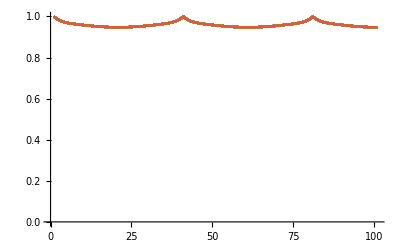

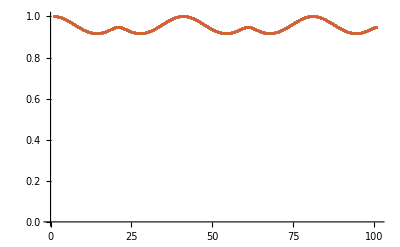

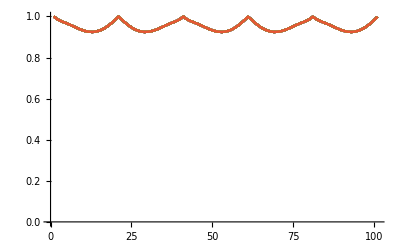

```mathematica
ListPlot[Table[V1,{t,0,π/2,π/200}],Joined->True,PlotRange->{0,Automatic}]
ListPlot[Table[V2,{t,0,π/2,π/200}],Joined->True,PlotRange->{0,Automatic}]
ListPlot[Table[V3,{t,0,π/2,π/200}],Joined->True,PlotRange->{0,Automatic}]
```

```mathematica
LogNeg1=Table[Max[0,-Log[Min[Abs[Eigenvalues[ⅈ Σ . σPT1]]]]],{t,0,π/2,π/200}];
LogNeg2=Table[Max[0,-Log[Min[Abs[Eigenvalues[ⅈ Σ . σPT2]]]]],{t,0,π/2,π/200}];
LogNeg3=Table[Max[0,-Log[Min[Abs[Eigenvalues[ⅈ Σ . σPT3]]]]],{t,0,π/2,π/200}];
```

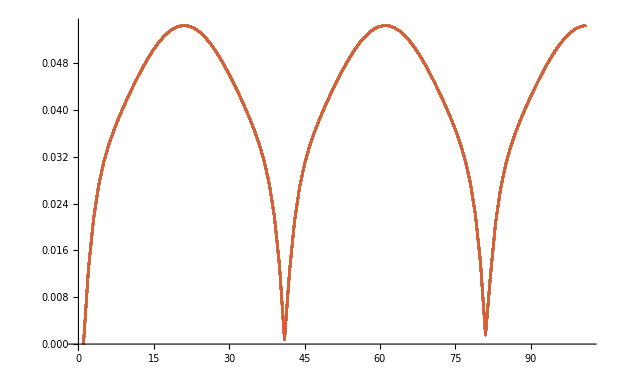

```mathematica
ListPlot[Table[LogNeg1,{t,0,π/2,π/200}],Joined->True,PlotRange->{0,Automatic}]
```

```mathematica
LogNeg1[[0]]
LogNeg1[[1]]
(*basically 0?*)
LogNeg1[[2]]
LogNeg1[[3]]
LogNeg1[[4]]
(*ALL non-zero. Therefore, bipartite entanglement between crystal and emitted field for 0 < t < 4*)
```

List

3.33067×10^-16

0.0129045

0.0213707

0.0269943

```mathematica
LogNeg1[[40]]
LogNeg1[[41]]
LogNeg1[[42]]
LogNeg1[[43]]
LogNeg1[[44]]
(*ALL non-zero. Therefore, bipartite entanglement between crystal and emitted field for 40 < t < 44*)
```

0.0134197

0.000779167

0.0123783

0.021026

0.0267602

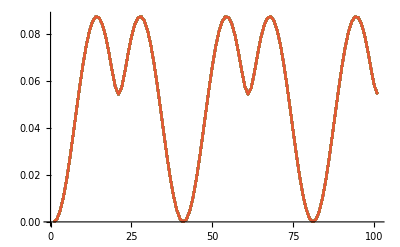

```mathematica
ListPlot[Table[LogNeg2,{t,0,π/2,π/200}],Joined->True,PlotRange->{0,Automatic}]
```

```mathematica
LogNeg2[[0]]
LogNeg2[[1]]
(*basically 0?*)
LogNeg2[[2]]
LogNeg2[[3]]
LogNeg2[[4]]
```

List

5.55112×10^-16

0.00122769

0.00483928

0.0106253

```mathematica
LogNeg2[[40]]
LogNeg2[[41]]
(*basically 0?*)
LogNeg2[[42]]
LogNeg2[[43]]
LogNeg2[[44]]
```

0.00135309

3.09581×10^-6

0.0011083

0.00460435

0.0102884

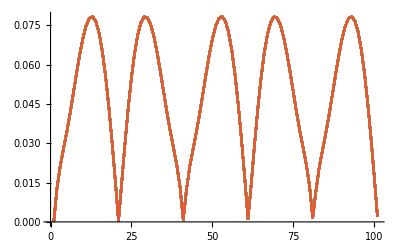

```mathematica
ListPlot[Table[LogNeg3,{t,0,π/2,π/200}],Joined->True,PlotRange->{0,Automatic}]
```

```mathematica
LogNeg3[[0]]
LogNeg3[[1]]
(*basically 0?*)
LogNeg3[[2]]
LogNeg3[[3]]
LogNeg3[[4]]
```

List

5.55112×10^-16

0.0128796

0.0214067

0.0278624

```mathematica
LogNeg3[[20]]
LogNeg3[[21]]
(*basically 0?*)
LogNeg3[[22]]
LogNeg3[[23]]
LogNeg3[[24]]
```

0.0159

0.000392906

0.0151365

0.0299268

0.0434111

```mathematica
LogNeg3[[40]]
LogNeg3[[41]]
(*basically 0?*)
LogNeg3[[42]]
LogNeg3[[43]]
LogNeg3[[44]]
```

0.0133924

0.000779161

0.0123557

0.0210482

0.0275546

```mathematica
LogNeg123=Table[CubeRoot[(Max[0,-Log[Min[Abs[Eigenvalues[ⅈ Σ . σPT1]]]]])(Max[0,-Log[Min[Abs[Eigenvalues[ⅈ Σ . σPT2]]]]])(Max[0,-Log[Min[Abs[Eigenvalues[ⅈ Σ . σPT3]]]]])],{t,0,π/2,π/200}]//Chop;
```

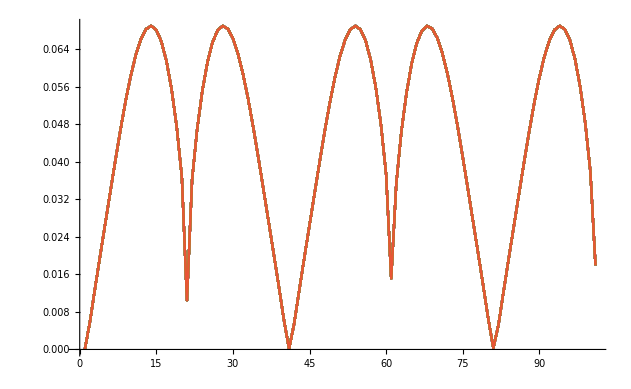

```mathematica
ListPlot[Table[LogNeg123,{t,0,π/2,π/200}],Joined->True,PlotRange->{0,Automatic}]
```